```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
ρ[x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}];
Subscript[ρ, B][x_,y_,t_]=1/b[t]*ρ[x/b[t],y/b[t]]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
Subscript[n, B][p_,t_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, B][x,y,t],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->5,PrecisionGoal->5];
```

```mathematica
Pdomain=Union[Range[0,2,1/4],Range[2,4,1/2]];
Tdomain = {0,0.25,.5,0.75,1,1.5,2,2.5,3,3.5,4,5,6,7,8,9,10,12};
(* Set interopolation functions for various points in time *)
Do[Subscript[dataSet, i]=Re[Subscript[n, B][Pdomain,Tdomain[[i]] ]];Subscript[dataSet, i],{i,1,Length[Tdomain]}]
(* Prepare domains and ranges for plotting*)
FullD=Flatten[Prepend[Take[Pdomain,-Length[Pdomain]+1],Reverse[-1*Pdomain]]];
Do[Subscript[FullR, i]=Flatten[Prepend[Take[Subscript[dataSet, i],-Length[Subscript[dataSet, i]]+1],Reverse[Subscript[dataSet, i]]]],{i,1,Length[Tdomain]}];
(* create list of interpolated functions for plotting purposes *)
Do[Subscript[f, i]=Interpolation[Thread[{FullD,Subscript[FullR, i]}] ],{i,1,Length[Tdomain]}]
```

$Aborted

InterpolatingFunction[…]

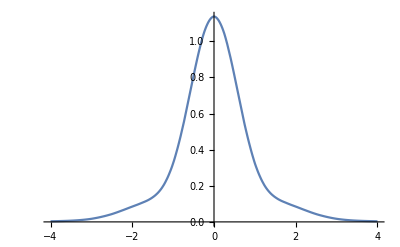

```mathematica
TestD=Union[Range[0,2,1/4],Range[2,4,1/2]];
TestR=Re[Subscript[n, B][TestD,12]];
FullD=Flatten[Prepend[Take[TestD,-Length[TestD]+1],Reverse[-1*TestD]]];
FullR=Flatten[Prepend[Take[TestR,-Length[TestR]+1],Reverse[TestR]]];
f=Interpolation[Thread[{FullD,FullR}]]
Plot[f[p],{p,-4,4}]
```